```mathematica
(* hydro + radiation coupled - works - implementing solver for deltas *)
```

```mathematica
(* perturbation *)
ρ=ρ0+δρ Exp[I (ω t-k x1)];
u=u0+δu Exp[I (ω t-k x1)];
u1=0+δu1 Exp[I (ω t-k x1)];
EE=EE0+δEE Exp[I (ω t-k x1)];
F1=0+δF1 Exp[I (ω t-k x1)];
```

```mathematica
(* stress tensor *)
T00=-(ρ+Γ u)+(Γ-1)u;
T10=-(ρ+Γ u)u1;
T01=(ρ+Γ u)u1;
T11=(ρ+Γ u)u1 u1+(Γ-1)u;
Rh00=EE; (* fluid frame *)
Rh01=F1;
Rh10=F1;
Rh11=1/3EE;
```

```mathematica
(* to zero higher orders in u and ρ *)
su2nd={
δu^2->0,
δu^3->0,
δu^4->0};
sρ2nd={
δρ^2->0,
δρ^3->0,
δρ^4->0};
```

```mathematica
(* to zero 2nd order *)
s2nd={
δu1 δu1->0,
δu1 δρ->0,
δu1 δu->0,
δu1 δEE->0,
δu1 δF1->0,
δρ δρ->0,
δρ δu->0,
δρ δu1->0,
δρ δEE->0,
δρ δF1->0,
δu δu->0,
δu δρ->0,
δu δu1->0,
δu δEE->0,
δu δF1->0
}
```

{δu1^2→0,δu1 δρ→0,δu δu1→0,δEE δu1→0,δF1 δu1→0,δρ^2→0,δu δρ→0,δu1 δρ→0,δEE δρ→0,δF1 δρ→0,δu^2→0,δu δρ→0,δu δu1→0,δEE δu→0,δF1 δu→0}

```mathematica
(* ideal gas equation of state *)
(* kb - reduced Boltzmann constant -> R *)
(* T4 = linearized T^4 *)
(* T4 perturbed *)
T4p=Expand[Normal[Series[(Expand[u^4](Γ-1)^4)/(kb^4 Expand[ρ^4]),{δu,0,1},{δρ,0,1}]]]/.s2nd
(* T4 unperturbed *)
T4u=(u0^4(Γ-1)^4)/(kb^4 ρ0^4);
(* LTE codnition *)
sLTE={EE0->4σ T4u};
```

-(4 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^4 δρ)/(kb^4 ρ0^5)+(16 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^4 Γ δρ)/(kb^4 ρ0^5)-(24 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^4 Γ^2 δρ)/(kb^4 ρ0^5)+(16 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^4 Γ^3 δρ)/(kb^4 ρ0^5)-(4 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^4 Γ^4 δρ)/(kb^4 ρ0^5)+u0^4/(kb^4 ρ0^4)-(4 u0^4 Γ)/(kb^4 ρ0^4)+(6 u0^4 Γ^2)/(kb^4 ρ0^4)-(4 u0^4 Γ^3)/(kb^4 ρ0^4)+(u0^4 Γ^4)/(kb^4 ρ0^4)+(4 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^3 δu)/(kb^4 ρ0^4)-(16 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^3 Γ δu)/(kb^4 ρ0^4)+(24 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^3 Γ^2 δu)/(kb^4 ρ0^4)-(16 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^3 Γ^3 δu)/(kb^4 ρ0^4)+(4 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^3 Γ^4 δu)/(kb^4 ρ0^4)

```mathematica
(* fluid frame to lab frame *)
(* perturbed *)
Ghcon0p=κ (EE-4σ T4p);
Ghcon1p=χ F1;
(* Lorentz boost *)
γ=1; (* if I want to relax δu1<<1 I also need to follow u^t; *)
Lp={{γ,u1},{u1,γ}};
Ghconp={Ghcon0p,Ghcon1p};
Gconp=0Ghconp;
For[i=1,i≤2,i++,
For[kk=1,kk≤2,kk++,
Gconp[[i]]=Gconp[[i]]+Lp[[i,kk]]Ghconp[[kk]];
]]
Gconp=Simplify[Expand[Gconp]/.s2nd];

(* unperturbed *)
Ghcon0u=κ(EE0-4σ T4u);
Ghcon1u=0;
γ=1;
Lu={{1,0},{0,1}};
Ghconu={Ghcon0u,Ghcon1u};
Gconu=0Ghconu;
For[i=1,i≤2,i++,
For[kk=1,kk≤2,kk++,
Gconu[[i]]=Gconu[[i]]+Lu[[i,kk]]Ghconu[[kk]];
]]
Gconu=Simplify[Expand[Gconu]/.s2nd];

(* difference *)
Gcon=Simplify[Expand[Simplify[Gconp-0Gconu]]/.s2nd];
Gcon0=Simplify[Gcon[[1]]]
Gcon1=Simplify[Gcon[[2]]]
Gcov0=-Gcon0;
Gcov1=Gcon1;
```

(ⅇ^(-ⅈ k x1) κ (ⅇ^(ⅈ k x1) ρ0 (EE0 kb^4 ρ0^4-4 u0^4 (-1+Γ)^4 σ)+ⅇ^(ⅈ t ω) (kb^4 δEE ρ0^5+16 u0^3 (-1+Γ)^4 (u0 δρ-δu ρ0) σ)))/(kb^4 ρ0^5)

(ⅇ^(-ⅈ (k x1-t ω)) (EE0 kb^4 δu1 κ ρ0^4-4 u0^4 (-1+Γ)^4 δu1 κ σ+kb^4 δF1 ρ0^4 χ))/(kb^4 ρ0^4)

```mathematica
(* radiation stress tensor transformation *)
Lp={{γ,u1},{u1,γ}};

Rh={{Rh00,Rh01},{Rh10,Rh11}};
R=0Rh;
For[i=1,i≤2,i++,
For[j=1,j≤2,j++,
For[kk=1,kk≤2,kk++,
For[l=1,l≤2,l++,
R[[i,j]]=R[[i,j]]+Lp[[i,kk]]Lp[[j,l]]Rh[[kk,l]];
]]]]

R=Expand[R]/.s2nd;
MatrixForm[R]

R00=-R[[1,1]];
R01=R[[1,2]];
R10=-R[[2,1]];
R11=R[[2,2]];
```

(EE0+ⅇ^(ⅈ (-k x1+t ω)) δEE | ⅇ^(ⅈ (-k x1+t ω)) δF1+4/3 ⅇ^(ⅈ (-k x1+t ω)) EE0 δu1
ⅇ^(ⅈ (-k x1+t ω)) δF1+4/3 ⅇ^(ⅈ (-k x1+t ω)) EE0 δu1 | EE0/3+1/3 ⅇ^(ⅈ (-k x1+t ω)) δEE)

```mathematica
(* equations *)
EQ1=D[ρ,t]+D[ρ u1,x1]==0
EQ2=D[T00,t]+D[T10,x1]+D[ρ,t]+D[ρ u1,x1]-Gcov0==0
EQ3=D[T01,t]+D[T11,x1]-Gcov1==0
EQ4=D[R00,t]+D[R10,x1]+Gcov0==0
EQ5=D[R01,t]+D[R11,x1]+Gcov1==0
```

-ⅈ ⅇ^(2 ⅈ (-k x1+t ω)) k δu1 δρ-ⅈ ⅇ^(ⅈ (-k x1+t ω)) k δu1 (ⅇ^(ⅈ (-k x1+t ω)) δρ+ρ0)+ⅈ ⅇ^(ⅈ (-k x1+t ω)) δρ ω==0

-ⅈ ⅇ^(2 ⅈ (-k x1+t ω)) k δu1 δρ+ⅇ^(ⅈ (-k x1+t ω)) δu1 (ⅈ ⅇ^(ⅈ (-k x1+t ω)) k Γ δu+ⅈ ⅇ^(ⅈ (-k x1+t ω)) k δρ)-ⅈ ⅇ^(ⅈ (-k x1+t ω)) k δu1 (-Γ (u0+ⅇ^(ⅈ (-k x1+t ω)) δu)-ⅇ^(ⅈ (-k x1+t ω)) δρ-ρ0)-ⅈ ⅇ^(ⅈ (-k x1+t ω)) k δu1 (ⅇ^(ⅈ (-k x1+t ω)) δρ+ρ0)+(ⅇ^(-ⅈ k x1) κ (ⅇ^(ⅈ k x1) ρ0 (EE0 kb^4 ρ0^4-4 u0^4 (-1+Γ)^4 σ)+ⅇ^(ⅈ t ω) (kb^4 δEE ρ0^5+16 u0^3 (-1+Γ)^4 (u0 δρ-δu ρ0) σ)))/(kb^4 ρ0^5)+ⅈ ⅇ^(ⅈ (-k x1+t ω)) (-1+Γ) δu ω-ⅈ ⅇ^(ⅈ (-k x1+t ω)) Γ δu ω==0

-ⅈ ⅇ^(ⅈ (-k x1+t ω)) k (-1+Γ) δu+ⅇ^(2 ⅈ (-k x1+t ω)) δu1^2 (-ⅈ ⅇ^(ⅈ (-k x1+t ω)) k Γ δu-ⅈ ⅇ^(ⅈ (-k x1+t ω)) k δρ)-2 ⅈ ⅇ^(2 ⅈ (-k x1+t ω)) k δu1^2 (Γ (u0+ⅇ^(ⅈ (-k x1+t ω)) δu)+ⅇ^(ⅈ (-k x1+t ω)) δρ+ρ0)-(ⅇ^(-ⅈ (k x1-t ω)) (EE0 kb^4 δu1 κ ρ0^4-4 u0^4 (-1+Γ)^4 δu1 κ σ+kb^4 δF1 ρ0^4 χ))/(kb^4 ρ0^4)+ⅈ ⅇ^(ⅈ (-k x1+t ω)) δu1 (Γ (u0+ⅇ^(ⅈ (-k x1+t ω)) δu)+ⅇ^(ⅈ (-k x1+t ω)) δρ+ρ0) ω+ⅇ^(ⅈ (-k x1+t ω)) δu1 (ⅈ ⅇ^(ⅈ (-k x1+t ω)) Γ δu ω+ⅈ ⅇ^(ⅈ (-k x1+t ω)) δρ ω)==0

ⅈ ⅇ^(ⅈ (-k x1+t ω)) k δF1+4/3 ⅈ ⅇ^(ⅈ (-k x1+t ω)) EE0 k δu1-(ⅇ^(-ⅈ k x1) κ (ⅇ^(ⅈ k x1) ρ0 (EE0 kb^4 ρ0^4-4 u0^4 (-1+Γ)^4 σ)+ⅇ^(ⅈ t ω) (kb^4 δEE ρ0^5+16 u0^3 (-1+Γ)^4 (u0 δρ-δu ρ0) σ)))/(kb^4 ρ0^5)-ⅈ ⅇ^(ⅈ (-k x1+t ω)) δEE ω==0

-1/3 ⅈ ⅇ^(ⅈ (-k x1+t ω)) k δEE+(ⅇ^(-ⅈ (k x1-t ω)) (EE0 kb^4 δu1 κ ρ0^4-4 u0^4 (-1+Γ)^4 δu1 κ σ+kb^4 δF1 ρ0^4 χ))/(kb^4 ρ0^4)+ⅈ ⅇ^(ⅈ (-k x1+t ω)) δF1 ω+4/3 ⅈ ⅇ^(ⅈ (-k x1+t ω)) EE0 δu1 ω==0

```mathematica
EQ11=Expand[EQ1]/.s2nd
EQ22=Expand[EQ2]/.s2nd
EQ33=Expand[EQ3]/.s2nd
EQ44=Expand[EQ4]/.s2nd
EQ55=Expand[EQ5]/.s2nd
```

-ⅈ ⅇ^(ⅈ (-k x1+t ω)) k δu1 ρ0+ⅈ ⅇ^(ⅈ (-k x1+t ω)) δρ ω==0

ⅈ ⅇ^(ⅈ (-k x1+t ω)) k u0 Γ δu1+EE0 κ+ⅇ^(-ⅈ k x1+ⅈ t ω) δEE κ+(16 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^4 δρ κ σ)/(kb^4 ρ0^5)-(64 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^4 Γ δρ κ σ)/(kb^4 ρ0^5)+(96 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^4 Γ^2 δρ κ σ)/(kb^4 ρ0^5)-(64 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^4 Γ^3 δρ κ σ)/(kb^4 ρ0^5)+(16 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^4 Γ^4 δρ κ σ)/(kb^4 ρ0^5)-(4 u0^4 κ σ)/(kb^4 ρ0^4)+(16 u0^4 Γ κ σ)/(kb^4 ρ0^4)-(24 u0^4 Γ^2 κ σ)/(kb^4 ρ0^4)+(16 u0^4 Γ^3 κ σ)/(kb^4 ρ0^4)-(4 u0^4 Γ^4 κ σ)/(kb^4 ρ0^4)-(16 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^3 δu κ σ)/(kb^4 ρ0^4)+(64 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^3 Γ δu κ σ)/(kb^4 ρ0^4)-(96 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^3 Γ^2 δu κ σ)/(kb^4 ρ0^4)+(64 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^3 Γ^3 δu κ σ)/(kb^4 ρ0^4)-(16 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^3 Γ^4 δu κ σ)/(kb^4 ρ0^4)-ⅈ ⅇ^(ⅈ (-k x1+t ω)) δu ω==0

ⅈ ⅇ^(ⅈ (-k x1+t ω)) k δu-ⅈ ⅇ^(ⅈ (-k x1+t ω)) k Γ δu-ⅇ^(-ⅈ (k x1-t ω)) EE0 δu1 κ+(4 ⅇ^(-ⅈ (k x1-t ω)) u0^4 δu1 κ σ)/(kb^4 ρ0^4)-(16 ⅇ^(-ⅈ (k x1-t ω)) u0^4 Γ δu1 κ σ)/(kb^4 ρ0^4)+(24 ⅇ^(-ⅈ (k x1-t ω)) u0^4 Γ^2 δu1 κ σ)/(kb^4 ρ0^4)-(16 ⅇ^(-ⅈ (k x1-t ω)) u0^4 Γ^3 δu1 κ σ)/(kb^4 ρ0^4)+(4 ⅇ^(-ⅈ (k x1-t ω)) u0^4 Γ^4 δu1 κ σ)/(kb^4 ρ0^4)-ⅇ^(-ⅈ (k x1-t ω)) δF1 χ+ⅈ ⅇ^(ⅈ (-k x1+t ω)) u0 Γ δu1 ω+ⅈ ⅇ^(ⅈ (-k x1+t ω)) δu1 ρ0 ω==0

ⅈ ⅇ^(ⅈ (-k x1+t ω)) k δF1+4/3 ⅈ ⅇ^(ⅈ (-k x1+t ω)) EE0 k δu1-EE0 κ-ⅇ^(-ⅈ k x1+ⅈ t ω) δEE κ-(16 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^4 δρ κ σ)/(kb^4 ρ0^5)+(64 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^4 Γ δρ κ σ)/(kb^4 ρ0^5)-(96 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^4 Γ^2 δρ κ σ)/(kb^4 ρ0^5)+(64 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^4 Γ^3 δρ κ σ)/(kb^4 ρ0^5)-(16 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^4 Γ^4 δρ κ σ)/(kb^4 ρ0^5)+(4 u0^4 κ σ)/(kb^4 ρ0^4)-(16 u0^4 Γ κ σ)/(kb^4 ρ0^4)+(24 u0^4 Γ^2 κ σ)/(kb^4 ρ0^4)-(16 u0^4 Γ^3 κ σ)/(kb^4 ρ0^4)+(4 u0^4 Γ^4 κ σ)/(kb^4 ρ0^4)+(16 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^3 δu κ σ)/(kb^4 ρ0^4)-(64 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^3 Γ δu κ σ)/(kb^4 ρ0^4)+(96 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^3 Γ^2 δu κ σ)/(kb^4 ρ0^4)-(64 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^3 Γ^3 δu κ σ)/(kb^4 ρ0^4)+(16 ⅇ^(-ⅈ k x1+ⅈ t ω) u0^3 Γ^4 δu κ σ)/(kb^4 ρ0^4)-ⅈ ⅇ^(ⅈ (-k x1+t ω)) δEE ω==0

-1/3 ⅈ ⅇ^(ⅈ (-k x1+t ω)) k δEE+ⅇ^(-ⅈ (k x1-t ω)) EE0 δu1 κ-(4 ⅇ^(-ⅈ (k x1-t ω)) u0^4 δu1 κ σ)/(kb^4 ρ0^4)+(16 ⅇ^(-ⅈ (k x1-t ω)) u0^4 Γ δu1 κ σ)/(kb^4 ρ0^4)-(24 ⅇ^(-ⅈ (k x1-t ω)) u0^4 Γ^2 δu1 κ σ)/(kb^4 ρ0^4)+(16 ⅇ^(-ⅈ (k x1-t ω)) u0^4 Γ^3 δu1 κ σ)/(kb^4 ρ0^4)-(4 ⅇ^(-ⅈ (k x1-t ω)) u0^4 Γ^4 δu1 κ σ)/(kb^4 ρ0^4)+ⅇ^(-ⅈ (k x1-t ω)) δF1 χ+ⅈ ⅇ^(ⅈ (-k x1+t ω)) δF1 ω+4/3 ⅈ ⅇ^(ⅈ (-k x1+t ω)) EE0 δu1 ω==0

```mathematica
EQ111=Simplify[EQ11[[1]]/ⅇ^(ⅈ (-k x1+t ω))/I]==0
EQ222=Simplify[EQ22[[1]]/ⅇ^(ⅈ (-k x1+t ω))/I]==0
EQ333=Simplify[EQ33[[1]]/ⅇ^(ⅈ (-k x1+t ω))/I]==0
EQ444=Simplify[EQ44[[1]]/ⅇ^(ⅈ (-k x1+t ω))/I]==0
EQ555=Simplify[EQ55[[1]]/ⅇ^(ⅈ (-k x1+t ω))/I]==0
EQS0={EQ111,EQ222,EQ333,EQ444,EQ555}/.sLTE
```

-k δu1 ρ0+δρ ω==0

(ⅇ^(-ⅈ t ω) (-ⅈ ⅇ^(ⅈ k x1) κ ρ0 (EE0 kb^4 ρ0^4-4 u0^4 (-1+Γ)^4 σ)+ⅇ^(ⅈ t ω) (k kb^4 u0 Γ δu1 ρ0^5-ⅈ (16 u0^3 (-1+Γ)^4 κ (u0 δρ-δu ρ0) σ+kb^4 ρ0^5 (δEE κ-ⅈ δu ω)))))/(kb^4 ρ0^5)==0

(-k kb^4 (-1+Γ) δu ρ0^4+ⅈ (EE0 kb^4 δu1 κ ρ0^4-4 u0^4 (-1+Γ)^4 δu1 κ σ-ⅈ kb^4 u0 Γ δu1 ρ0^4 ω+kb^4 ρ0^4 (δF1 χ-ⅈ δu1 ρ0 ω)))/(kb^4 ρ0^4)==0

(ⅇ^(-ⅈ t ω) (3 ⅈ ⅇ^(ⅈ k x1) κ ρ0 (EE0 kb^4 ρ0^4-4 u0^4 (-1+Γ)^4 σ)+ⅇ^(ⅈ t ω) (k kb^4 (3 δF1+4 EE0 δu1) ρ0^5+3 ⅈ (16 u0^3 (-1+Γ)^4 κ (u0 δρ-δu ρ0) σ+kb^4 δEE ρ0^5 (κ+ⅈ ω)))))/(3 kb^4 ρ0^5)==0

-(ⅈ (-ⅈ k kb^4 δEE ρ0^4+3 (-4 u0^4 (-1+Γ)^4 δu1 κ σ+kb^4 δF1 ρ0^4 (χ+ⅈ ω))+EE0 kb^4 δu1 ρ0^4 (3 κ+4 ⅈ ω)))/(3 kb^4 ρ0^4)==0

{-k δu1 ρ0+δρ ω==0,(k kb^4 u0 Γ δu1 ρ0^5-ⅈ (16 u0^3 (-1+Γ)^4 κ (u0 δρ-δu ρ0) σ+kb^4 ρ0^5 (δEE κ-ⅈ δu ω)))/(kb^4 ρ0^5)==0,(-k kb^4 (-1+Γ) δu ρ0^4+ⅈ (-ⅈ kb^4 u0 Γ δu1 ρ0^4 ω+kb^4 ρ0^4 (δF1 χ-ⅈ δu1 ρ0 ω)))/(kb^4 ρ0^4)==0,(k kb^4 ρ0^5 (3 δF1+(16 u0^4 (-1+Γ)^4 δu1 σ)/(kb^4 ρ0^4))+3 ⅈ (16 u0^3 (-1+Γ)^4 κ (u0 δρ-δu ρ0) σ+kb^4 δEE ρ0^5 (κ+ⅈ ω)))/(3 kb^4 ρ0^5)==0,-(ⅈ (-ⅈ k kb^4 δEE ρ0^4+3 (-4 u0^4 (-1+Γ)^4 δu1 κ σ+kb^4 δF1 ρ0^4 (χ+ⅈ ω))+4 u0^4 (-1+Γ)^4 δu1 σ (3 κ+4 ⅈ ω)))/(3 kb^4 ρ0^4)==0}

```mathematica
(* linearized set in matrix form *)
AAA=Array[0#1&,{5,5}];
AAA[[1,1]]=Coefficient[EQ111[[1]],δρ];
AAA[[1,2]]=Coefficient[EQ111[[1]],δu1];
AAA[[1,3]]=Coefficient[EQ111[[1]],δu];
AAA[[1,4]]=Coefficient[EQ111[[1]],δEE];
AAA[[1,5]]=Coefficient[EQ111[[1]],δF1];
AAA[[2,1]]=Coefficient[EQ333[[1]],δρ];
AAA[[2,2]]=Coefficient[EQ333[[1]],δu1];
AAA[[2,3]]=Coefficient[EQ333[[1]],δu];
AAA[[2,4]]=Coefficient[EQ333[[1]],δEE];
AAA[[2,5]]=Coefficient[EQ333[[1]],δF1];
AAA[[3,1]]=Coefficient[EQ222[[1]],δρ];
AAA[[3,2]]=Coefficient[EQ222[[1]],δu1];
AAA[[3,3]]=Coefficient[EQ222[[1]],δu];
AAA[[3,4]]=Coefficient[EQ222[[1]],δEE];
AAA[[3,5]]=Coefficient[EQ222[[1]],δF1];
AAA[[4,1]]=Coefficient[EQ444[[1]],δρ];
AAA[[4,2]]=Coefficient[EQ444[[1]],δu1];
AAA[[4,3]]=Coefficient[EQ444[[1]],δu];
AAA[[4,4]]=Coefficient[EQ444[[1]],δEE];
AAA[[4,5]]=Coefficient[EQ444[[1]],δF1];
AAA[[5,1]]=Coefficient[EQ555[[1]],δρ];
AAA[[5,2]]=Coefficient[EQ555[[1]],δu1];
AAA[[5,3]]=Coefficient[EQ555[[1]],δu];
AAA[[5,4]]=Coefficient[EQ555[[1]],δEE];
AAA[[5,5]]=Coefficient[EQ555[[1]],δF1];
```

```mathematica
MatrixForm[Simplify[AAA/.sLTE]]
```

(ω | -k ρ0 | 0 | 0 | 0
0 | (u0 Γ+ρ0) ω | k-k Γ | 0 | ⅈ χ
-(16 ⅈ u0^4 (-1+Γ)^4 κ σ)/(kb^4 ρ0^5) | k u0 Γ | (ⅈ (16 u0^3 (-1+Γ)^4 κ σ+ⅈ kb^4 ρ0^4 ω))/(kb^4 ρ0^4) | -ⅈ κ | 0
(16 ⅈ u0^4 (-1+Γ)^4 κ σ)/(kb^4 ρ0^5) | (16 k u0^4 (-1+Γ)^4 σ)/(3 kb^4 ρ0^4) | -(16 ⅈ u0^3 (-1+Γ)^4 κ σ)/(kb^4 ρ0^4) | ⅈ κ-ω | k
0 | (16 u0^4 (-1+Γ)^4 σ ω)/(3 kb^4 ρ0^4) | 0 | -k/3 | -ⅈ χ+ω)

```mathematica
MatrixForm[Simplify[AAA/.{κ->0,χ->0}/.sLTE]]
```

(ω | -k ρ0 | 0 | 0 | 0
0 | (u0 Γ+ρ0) ω | k-k Γ | 0 | 0
0 | k u0 Γ | -ω | 0 | 0
0 | (16 k u0^4 (-1+Γ)^4 σ)/(3 kb^4 ρ0^4) | 0 | -ω | k
0 | (16 u0^4 (-1+Γ)^4 σ ω)/(3 kb^4 ρ0^4) | 0 | -k/3 | ω)

```mathematica
(* matrix determinant -> dispersion relation *)
DIS1=Det[AAA/.sLTE]==0
```

k ρ0 ((16 ⅈ k^3 u0^4 κ σ)/(3 kb^4 ρ0^5)-(80 ⅈ k^3 u0^4 Γ κ σ)/(3 kb^4 ρ0^5)+(160 ⅈ k^3 u0^4 Γ^2 κ σ)/(3 kb^4 ρ0^5)-(160 ⅈ k^3 u0^4 Γ^3 κ σ)/(3 kb^4 ρ0^5)+(80 ⅈ k^3 u0^4 Γ^4 κ σ)/(3 kb^4 ρ0^5)-(16 ⅈ k^3 u0^4 Γ^5 κ σ)/(3 kb^4 ρ0^5)-(64 k u0^4 κ σ χ ω)/(3 kb^4 ρ0^5)+(304 k u0^4 Γ κ σ χ ω)/(3 kb^4 ρ0^5)-(192 k u0^4 Γ^2 κ σ χ ω)/(kb^4 ρ0^5)+(544 k u0^4 Γ^3 κ σ χ ω)/(3 kb^4 ρ0^5)-(256 k u0^4 Γ^4 κ σ χ ω)/(3 kb^4 ρ0^5)+(16 k u0^4 Γ^5 κ σ χ ω)/(kb^4 ρ0^5)-(16 ⅈ k u0^4 κ σ ω^2)/(kb^4 ρ0^5)+(80 ⅈ k u0^4 Γ κ σ ω^2)/(kb^4 ρ0^5)-(160 ⅈ k u0^4 Γ^2 κ σ ω^2)/(kb^4 ρ0^5)+(160 ⅈ k u0^4 Γ^3 κ σ ω^2)/(kb^4 ρ0^5)-(80 ⅈ k u0^4 Γ^4 κ σ ω^2)/(kb^4 ρ0^5)+(16 ⅈ k u0^4 Γ^5 κ σ ω^2)/(kb^4 ρ0^5))+ω (-1/3 k^4 u0 Γ+1/3 k^4 u0 Γ^2-k^2 u0 Γ κ χ+k^2 u0 Γ^2 κ χ-(16 k^2 u0^4 κ σ χ)/(3 kb^4 ρ0^4)+(32 k^2 u0^4 Γ κ σ χ)/(kb^4 ρ0^4)-(224 k^2 u0^4 Γ^2 κ σ χ)/(3 kb^4 ρ0^4)+(256 k^2 u0^4 Γ^3 κ σ χ)/(3 kb^4 ρ0^4)-(48 k^2 u0^4 Γ^4 κ σ χ)/(kb^4 ρ0^4)+(32 k^2 u0^4 Γ^5 κ σ χ)/(3 kb^4 ρ0^4)+(256 k^2 u0^7 κ σ^2 χ)/(9 kb^8 ρ0^8)-(2048 k^2 u0^7 Γ κ σ^2 χ)/(9 kb^8 ρ0^8)+(7168 k^2 u0^7 Γ^2 κ σ^2 χ)/(9 kb^8 ρ0^8)-(14336 k^2 u0^7 Γ^3 κ σ^2 χ)/(9 kb^8 ρ0^8)+(17920 k^2 u0^7 Γ^4 κ σ^2 χ)/(9 kb^8 ρ0^8)-(14336 k^2 u0^7 Γ^5 κ σ^2 χ)/(9 kb^8 ρ0^8)+(7168 k^2 u0^7 Γ^6 κ σ^2 χ)/(9 kb^8 ρ0^8)-(2048 k^2 u0^7 Γ^7 κ σ^2 χ)/(9 kb^8 ρ0^8)+(256 k^2 u0^7 Γ^8 κ σ^2 χ)/(9 kb^8 ρ0^8)-ⅈ k^2 u0 Γ κ ω+ⅈ k^2 u0 Γ^2 κ ω+(16 ⅈ k^2 u0^4 Γ κ σ ω)/(3 kb^4 ρ0^4)-(64 ⅈ k^2 u0^4 Γ^2 κ σ ω)/(3 kb^4 ρ0^4)+(32 ⅈ k^2 u0^4 Γ^3 κ σ ω)/(kb^4 ρ0^4)-(64 ⅈ k^2 u0^4 Γ^4 κ σ ω)/(3 kb^4 ρ0^4)+(16 ⅈ k^2 u0^4 Γ^5 κ σ ω)/(3 kb^4 ρ0^4)+(16 ⅈ k^2 u0^3 κ σ ω)/(3 kb^4 ρ0^3)-(64 ⅈ k^2 u0^3 Γ κ σ ω)/(3 kb^4 ρ0^3)+(32 ⅈ k^2 u0^3 Γ^2 κ σ ω)/(kb^4 ρ0^3)-(64 ⅈ k^2 u0^3 Γ^3 κ σ ω)/(3 kb^4 ρ0^3)+(16 ⅈ k^2 u0^3 Γ^4 κ σ ω)/(3 kb^4 ρ0^3)-ⅈ k^2 u0 Γ χ ω+ⅈ k^2 u0 Γ^2 χ ω+(16 ⅈ k^2 u0^4 σ χ ω)/(9 kb^4 ρ0^4)-(64 ⅈ k^2 u0^4 Γ σ χ ω)/(9 kb^4 ρ0^4)+(32 ⅈ k^2 u0^4 Γ^2 σ χ ω)/(3 kb^4 ρ0^4)-(64 ⅈ k^2 u0^4 Γ^3 σ χ ω)/(9 kb^4 ρ0^4)+(16 ⅈ k^2 u0^4 Γ^4 σ χ ω)/(9 kb^4 ρ0^4)+2/3 k^2 u0 Γ ω^2-k^2 u0 Γ^2 ω^2-1/3 k^2 ρ0 ω^2-u0 Γ κ χ ω^2-κ ρ0 χ ω^2-(16 u0^4 κ σ χ ω^2)/(3 kb^4 ρ0^4)+(16 u0^4 Γ κ σ χ ω^2)/(3 kb^4 ρ0^4)+(32 u0^4 Γ^2 κ σ χ ω^2)/(kb^4 ρ0^4)-(224 u0^4 Γ^3 κ σ χ ω^2)/(3 kb^4 ρ0^4)+(176 u0^4 Γ^4 κ σ χ ω^2)/(3 kb^4 ρ0^4)-(16 u0^4 Γ^5 κ σ χ ω^2)/(kb^4 ρ0^4)-(16 u0^3 κ σ χ ω^2)/(kb^4 ρ0^3)+(64 u0^3 Γ κ σ χ ω^2)/(kb^4 ρ0^3)-(96 u0^3 Γ^2 κ σ χ ω^2)/(kb^4 ρ0^3)+(64 u0^3 Γ^3 κ σ χ ω^2)/(kb^4 ρ0^3)-(16 u0^3 Γ^4 κ σ χ ω^2)/(kb^4 ρ0^3)-(256 u0^7 κ σ^2 χ ω^2)/(3 kb^8 ρ0^8)+(2048 u0^7 Γ κ σ^2 χ ω^2)/(3 kb^8 ρ0^8)-(7168 u0^7 Γ^2 κ σ^2 χ ω^2)/(3 kb^8 ρ0^8)+(14336 u0^7 Γ^3 κ σ^2 χ ω^2)/(3 kb^8 ρ0^8)-(17920 u0^7 Γ^4 κ σ^2 χ ω^2)/(3 kb^8 ρ0^8)+(14336 u0^7 Γ^5 κ σ^2 χ ω^2)/(3 kb^8 ρ0^8)-(7168 u0^7 Γ^6 κ σ^2 χ ω^2)/(3 kb^8 ρ0^8)+(2048 u0^7 Γ^7 κ σ^2 χ ω^2)/(3 kb^8 ρ0^8)-(256 u0^7 Γ^8 κ σ^2 χ ω^2)/(3 kb^8 ρ0^8)-ⅈ u0 Γ κ ω^3-ⅈ κ ρ0 ω^3-(16 ⅈ u0^4 Γ κ σ ω^3)/(kb^4 ρ0^4)+(64 ⅈ u0^4 Γ^2 κ σ ω^3)/(kb^4 ρ0^4)-(96 ⅈ u0^4 Γ^3 κ σ ω^3)/(kb^4 ρ0^4)+(64 ⅈ u0^4 Γ^4 κ σ ω^3)/(kb^4 ρ0^4)-(16 ⅈ u0^4 Γ^5 κ σ ω^3)/(kb^4 ρ0^4)-(16 ⅈ u0^3 κ σ ω^3)/(kb^4 ρ0^3)+(64 ⅈ u0^3 Γ κ σ ω^3)/(kb^4 ρ0^3)-(96 ⅈ u0^3 Γ^2 κ σ ω^3)/(kb^4 ρ0^3)+(64 ⅈ u0^3 Γ^3 κ σ ω^3)/(kb^4 ρ0^3)-(16 ⅈ u0^3 Γ^4 κ σ ω^3)/(kb^4 ρ0^3)-ⅈ u0 Γ χ ω^3-ⅈ ρ0 χ ω^3-(16 ⅈ u0^4 σ χ ω^3)/(3 kb^4 ρ0^4)+(64 ⅈ u0^4 Γ σ χ ω^3)/(3 kb^4 ρ0^4)-(32 ⅈ u0^4 Γ^2 σ χ ω^3)/(kb^4 ρ0^4)+(64 ⅈ u0^4 Γ^3 σ χ ω^3)/(3 kb^4 ρ0^4)-(16 ⅈ u0^4 Γ^4 σ χ ω^3)/(3 kb^4 ρ0^4)+u0 Γ ω^4+ρ0 ω^4)==0

```mathematica
DIS2=Simplify[DIS1][[1]]==0
```

1/(kb ρ0)(-3 (16 u0^3 (-1+Γ)^4 κ σ+kb^4 ρ0^4 (κ+ⅈ ω)) (16 u0^4 (-1+Γ)^4 σ χ+3 kb^4 ρ0^4 (u0 Γ+ρ0) (χ+ⅈ ω)) ω^3-3 ⅈ k^4 kb^4 u0 (-1+Γ) ρ0^4 (16 u0^3 (-1+Γ)^4 κ σ+ⅈ kb^4 Γ ρ0^4 ω)+k^2 ω (256 u0^7 (-1+Γ)^8 κ σ^2 χ-3 kb^8 ρ0^8 (ρ0 ω^2+u0 Γ (-3 (-1+Γ) κ (χ+ⅈ ω)+ω (-3 ⅈ (-1+Γ) χ+(-2+3 Γ) ω)))+16 kb^4 u0^3 (-1+Γ)^4 ρ0^4 σ (3 ⅈ κ ρ0 ω+u0 (ⅈ χ ω+3 κ (5 (-1+Γ) χ+ⅈ (-3+4 Γ) ω)))))==0

```mathematica
solω=Solve[DIS2,ω];
solk=Solve[DIS2,k];
```

```mathematica
(*Simplify[solk]*)
```

```mathematica
GGG=6.674 10^-8;
CCC=2.998 10^10;
(* CC,PP to σ and u0 *)
radnum[CC_,PP_]:={

Γtu=5/3;
kbtu=(1.3806488 10^-16 GGG/CCC^4)/(1 1.6726215 10^-24 GGG/CCC^2);
ρ0tu=1;
u0tu=1/(CC^2 Γtu(Γtu-1-1/CC^2));
Ttu=(u0tu(Γtu-1))/(kbtu ρ0tu);
σtu=(PP(Γtu-1)u0tu)/(4/1 Ttu^4);
E0tu=4σtu Ttu^4;
r=(Γtu-1)PP/(4Γtu);
Bo=(4 √Γtu Γtu)/(PP CC(Γtu-1));
a=√(Γtu(Γtu-1)u0tu/(ρ0tu+Γtu u0tu));
{ρ0tu,u0tu,σtu,Ttu,r,Bo,a,E0tu}
}
```

```mathematica
(* here you define [CC,PP] and kappa *)
kappa=0.01;
out=radnum[10^2,0.01]
a0=out[[1,7]];
subnum={
ρ0->1,
u0->N[out[[1,2]]],
σ->N[out[[1,3]]],
Γ-> 5/3,
kb-> (1.3806488 10^-16 GGG/CCC^4)/(1 1.6726215 10^-24 GGG/CCC^2),
χ->κ,
κ->κ,
EE0->N[out[[1,8]]],
T0->N[out[[1,4]]]
}
```

{{1,9/99985,8.22962×10^-43,6.53423×10^8,0.001,12.9099,1/100,6.0009×10^-7}}

{ρ0→1,u0→0.0000900135,σ→8.22962×10^-43,Γ→5/3,kb→9.1838×10^-14,χ→κ,κ→κ,EE0→6.0009×10^-7,T0→6.53423×10^8}

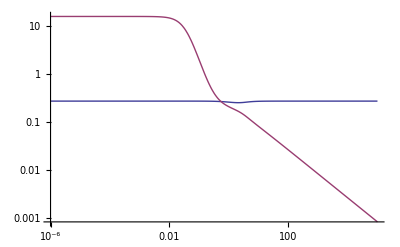

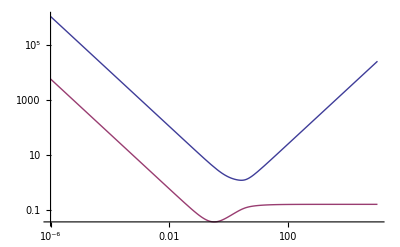

```mathematica
ssac[κ_]:=Evaluate[(1/(solk[[4,1,2]]/.{ω->3.62}/.subnum))]
ssra[κ_]:=Evaluate[(1/(solk[[2,1,2]]/.{ω->3.62}/.subnum))]
LogLogPlot[{Re[ssac[t/a0]]/a0,Re[ssra[t/a0]]/a0},{t,0.000001,100000},PlotRange->{-1,1}]
LogLogPlot[{Re[ssac[t/a0]]/Im[ssac[t/a0]]/(2π),Re[ssra[t/a0]]/Im[ssra[t/a0]]/(2π)},{t,0.000001,100000},PlotRange->{-1,1}]
```

```mathematica
ssω0[kk_]:=NSolve[DIS2/.subnum/.{k->2π,κ->kk},ω]
```

```mathematica
drho=10^-3;
EQS1=EQS0/.subnum/.{k->2π}/.ssω0[kappa][[1]]/.{κ->kappa}/.{δρ->drho};
EQS2=EQS0/.subnum/.{k->2π}/.ssω0[kappa][[2]]/.{κ->kappa}/.{δρ->drho};
EQS3=EQS0/.subnum/.{k->2π}/.ssω0[kappa][[3]]/.{κ->kappa}/.{δρ->drho};
EQS4=EQS0/.subnum/.{k->2π}/.ssω0[kappa][[4]]/.{κ->kappa}/.{δρ->drho};
EQS5=EQS0/.subnum/.{k->2π}/.ssω0[kappa][[5]]/.{κ->kappa}/.{δρ->drho};
deltas=TableForm[{
Quiet[Join[{ω->ssω0[kappa][[1,1,2]]},{v[c]->ssω0[kappa][[1,1,2]]/(2π)},{"v[a]"->ssω0[kappa][[1,1,2]]/(2π)/a0},{δρ->drho},Quiet[Solve[Evaluate[EQS1],{δu,δu1,δEE,δF1}]][[1]]]],
Quiet[Join[{ω->ssω0[kappa][[2,1,2]]},{v[c]->ssω0[kappa][[2,1,2]]/(2π)},{"v[a]"->ssω0[kappa][[2,1,2]]/(2π)/a0},{δρ->drho},Quiet[Solve[Evaluate[EQS2],{δu,δu1,δEE,δF1}]][[1]]]],Quiet[Join[{ω->ssω0[kappa][[3,1,2]]},{v[c]->ssω0[kappa][[3,1,2]]/(2π)},{"v[a]"->ssω0[kappa][[3,1,2]]/(2π)/a0},{δρ->drho},Quiet[Solve[Evaluate[EQS3],{δu,δu1,δEE,δF1}]][[1]]]],Quiet[Join[{ω->ssω0[kappa][[4,1,2]]},{v[c]->ssω0[kappa][[4,1,2]]/(2π)},{"v[a]"->ssω0[kappa][[4,1,2]]/(2π)/a0},{δρ->drho},Quiet[Solve[Evaluate[EQS4],{δu,δu1,δEE,δF1}]][[1]]]],Quiet[Join[{ω->ssω0[kappa][[5,1,2]]},{v[c]->ssω0[kappa][[5,1,2]]/(2π)},{"v[a]"->ssω0[kappa][[5,1,2]]/(2π)/a0},{δρ->drho},Quiet[Solve[Evaluate[EQS5],{δu,δu1,δEE,δF1}]][[1]]]]
}]
```

ω→-3.6276+0.01 ⅈ | v[c]→-0.57735+0.00159155 ⅈ | v[a]→-57.735+0.159155 ⅈ | δρ→1/1000 | δu→0.000333432-1.53996×10^-6 ⅈ | δu1→-0.00057735+1.59155×10^-6 ⅈ | δEE→-0.000883028-0.1209 ⅈ | δF1→0.000509817+0.0698016 ⅈ
ω→-0.0628317+0.0000533366 ⅈ | v[c]→-0.00999998+8.48878×10^-6 ⅈ | v[a]→-0.999998+0.000848878 ⅈ | δρ→1/1000 | δu→1.50022×10^-7-2.54682×10^-10 ⅈ | δu1→-9.99998×10^-6+8.48878×10^-9 ⅈ | δEE→1.1753×10^-14-1.14691×10^-13 ⅈ | δF1→8.01169×10^-12+2.54116×10^-12 ⅈ
ω→0.+0.000159999 ⅈ | v[c]→0.+0.0000254647 ⅈ | v[a]→0.+0.00254647 ⅈ | δρ→1/1000 | δu→-9.63654×10^-13+0. ⅈ | δu1→0.+2.54647×10^-8 ⅈ | δEE→-1.8046×10^-14+0. ⅈ | δF1→0.-3.84068×10^-12 ⅈ
ω→0.0628317+0.0000533366 ⅈ | v[c]→0.00999998+8.48878×10^-6 ⅈ | v[a]→0.999998+0.000848878 ⅈ | δρ→1/1000 | δu→1.50022×10^-7+2.54682×10^-10 ⅈ | δu1→9.99998×10^-6+8.48878×10^-9 ⅈ | δEE→1.1753×10^-14+1.14691×10^-13 ⅈ | δF1→-8.01169×10^-12+2.54116×10^-12 ⅈ
ω→3.6276+0.01 ⅈ | v[c]→0.57735+0.00159155 ⅈ | v[a]→57.735+0.159155 ⅈ | δρ→1/1000 | δu→0.000333432+1.53996×10^-6 ⅈ | δu1→0.00057735+1.59155×10^-6 ⅈ | δEE→-0.000883028+0.1209 ⅈ | δF1→-0.000509817+0.0698016 ⅈ

```mathematica
subnum
```

{ρ0→1,u0→0.0000900135,σ→8.22962×10^-43,Γ→5/3,kb→9.1838×10^-14,χ→κ,κ→κ,EE0→6.0009×10^-7,T0→6.53423×10^8}

```mathematica
ssω0[kappa]
```

{{ω→-3.6276+0.01 ⅈ},{ω→-0.0628317+0.0000533366 ⅈ},{ω→0.+0.000159999 ⅈ},{ω→0.0628317+0.0000533366 ⅈ},{ω→3.6276+0.01 ⅈ}}

```mathematica
Solve[Evaluate[EQS4],{δu,δu1,δEE,δF1}][[1,1,2]]/(u0/.subnum)
Solve[Evaluate[EQS4],{δu,δu1,δEE,δF1}][[1,2,2]]
Solve[Evaluate[EQS4],{δu,δu1,δEE,δF1}][[1,3,2]]/(EE0/.subnum)
Solve[Evaluate[EQS4],{δu,δu1,δEE,δF1}][[1,4,2]]/(EE0/.subnum)
Solve[Evaluate[EQS4],{δu,δu1,δEE,δF1}][[1,1,2]]
Solve[Evaluate[EQS4],{δu,δu1,δEE,δF1}][[1,2,2]]
Solve[Evaluate[EQS4],{δu,δu1,δEE,δF1}][[1,3,2]]
Solve[Evaluate[EQS4],{δu,δu1,δEE,δF1}][[1,4,2]]
```

0.00166666+2.82938×10^-6 ⅈ

9.99998×10^-6+8.48878×10^-9 ⅈ

1.95853×10^-8+1.91123×10^-7 ⅈ

-0.0000133508+4.23463×10^-6 ⅈ

1.50022×10^-7+2.54682×10^-10 ⅈ

9.99998×10^-6+8.48878×10^-9 ⅈ

1.1753×10^-14+1.14691×10^-13 ⅈ

-8.01169×10^-12+2.54116×10^-12 ⅈ

```mathematica
nsol=4;
{N[out[[1,1]]] ,deltas[[1,nsol,4,2]]/out[[1,1]] } (* δρ/ρ *)
{0,deltas[[1,nsol,6,2]] } (* δu1/u1 *)
{N[out[[1,2]]] ,deltas[[1,nsol,5,2]]/out[[1,2]] } (* δu/u *)
{N[out[[1,8]]] ,deltas[[1,nsol,7,2]]/out[[1,8]]}(* δE/E *)
{N[out[[1,8]]] ,deltas[[1,nsol,8,2]]/out[[1,8]]}(* δF/E *)
{deltas[[1,nsol,1,2]]} (* ω *)
```

{1.,1/1000}

{0,9.99998×10^-6+8.48878×10^-9 ⅈ}

{0.0000900135,0.00166666+2.82938×10^-6 ⅈ}

{6.0009×10^-7,1.95853×10^-8+1.91123×10^-7 ⅈ}

{6.0009×10^-7,-0.0000133508+4.23463×10^-6 ⅈ}

{0.0628317+0.0000533366 ⅈ}